#### gr. 1

Zad. 1

```mathematica
Together[3/(x+1)-2/(x-1)+1/(x+2)];
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
```

(-11-3 x+2 x^2)/(-2-x+2 x^2+x^3)

-2 Log[1-x]+3 Log[1+x]+Log[2+x]

Zad. 2

-4+x^2

{{x→-2},{x→2}}

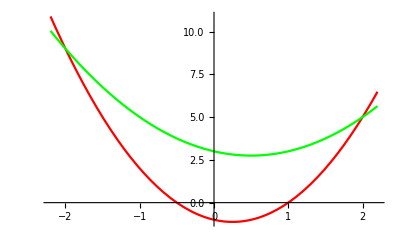

32/3

```mathematica
(x-2)(x+2)//Expand
y1=2 x^2-x-1;
y2=x^2-x+3;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-2.2,2.2},PlotStyle->{Red,Green}]
Integrate[y2-y1,{x,-2,2}]
```

Zad. 3

```mathematica
z=x^3-2 x y+y^2-5 x;
D[z,x]
D[z,y]
pk=Solve[{D[z,x]==0,D[z,y]==0},{x,y}]
H=Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}];
H/.pk
D[z,x,x]/.pk
```

-5+3 x^2-2 y

-2 x+2 y

{{x→-1,y→-1},{x→5/3,y→5/3}}

{-16,16}

{-6,10}

#### gr. 2

Zad. 1

```mathematica
Together[4/(x-3)+(x-3)/(x^2+1)]
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
```

(13-6 x+5 x^2)/((-3+x) (1+x^2))

(13-6 x+5 x^2)/(-3+x-3 x^2+x^3)

-3 ArcTan[x]+4 Log[3-x]+1/2 Log[1+x^2]

Zad. 2

```mathematica
π Integrate[(1/x^2)^2,{x,1,2}]
```

(7 π)/24

Zad. 3

```mathematica
z=(2x-3y-1)^2+(3x-2y-4)^2;
D[z,x]//Expand
D[z,y]//Expand
pk=Solve[{D[z,x]==0,D[z,y]==0},{x,y}]
H=Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}];
H/.pk
D[z,x,x]/.pk
```

-28+26 x-24 y

22-24 x+26 y

{{x→2,y→1}}

{100}

{26}